# ApplyGraphEmbeddings

Apply all graph embeddings to a graph to the graph from different vantage points

## Definition

```mathematica
ApplyGraphEmbeddings[graph_?GraphQ]:=AssociationMap[embedding↦Graph,{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","SpiralEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","PlanarEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}]
```

## Documentation

### Usage

ApplyGraphEmbeddings[graph]

see all possible graph embeddings applied to graph.

### Details & Options

The graph embeddings might be identical.

The graph embedding dimension is set to 2 for a plane. 3D graph embeddings can be created with Graph3D and GraphEmbedding, which has an argument for the dimension.

## Examples

### Basic Examples

See different embeddings for a bipartite graph:

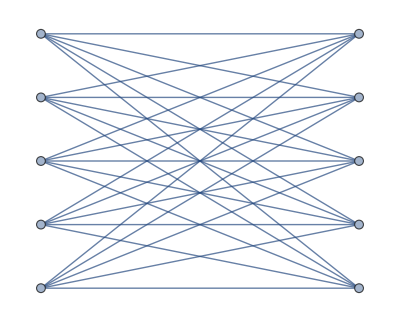
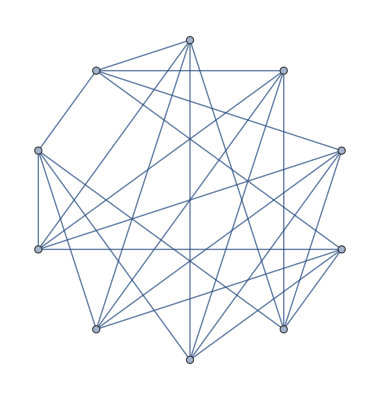
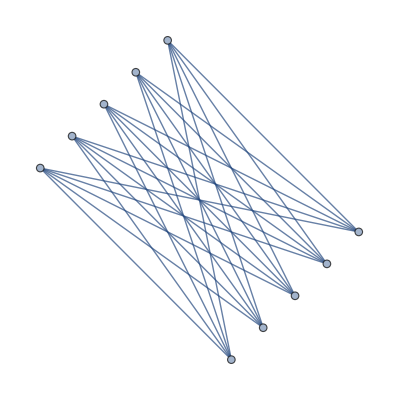
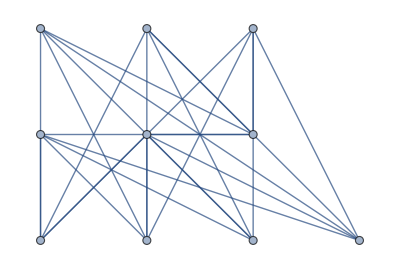
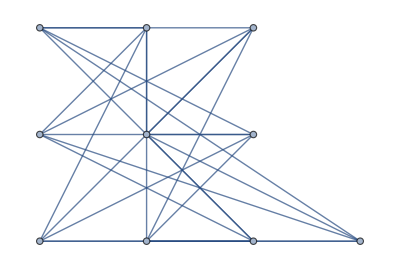
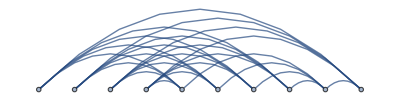
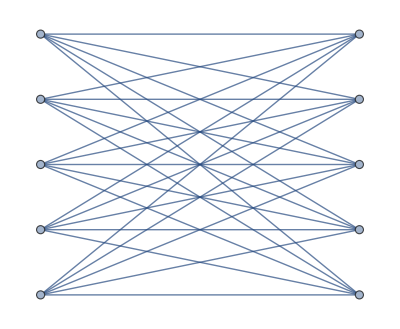
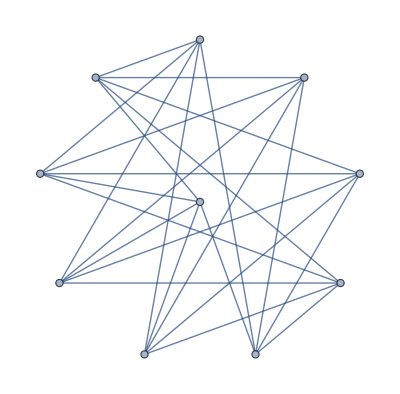
<|BipartiteEmbedding→-Graphics-,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→|>

```mathematica
ApplyGraphEmbeddings[CompleteGraph[{5,5}]]
```

Apply graph embeddings to three dimensional graph, the Buckyball graph:

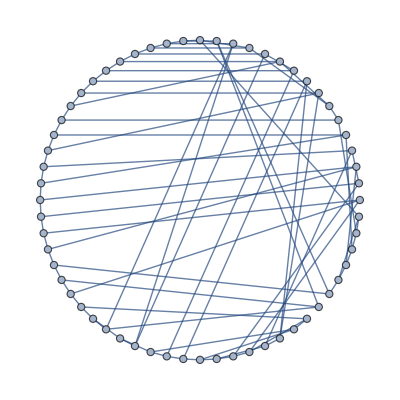
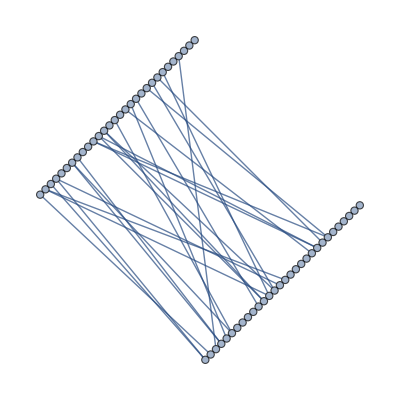
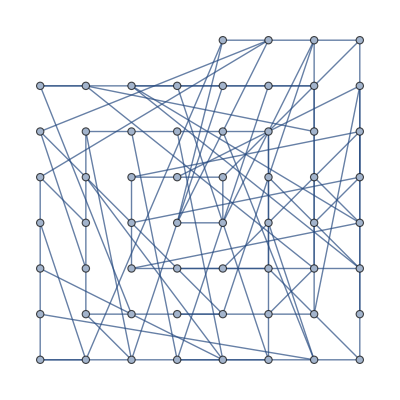
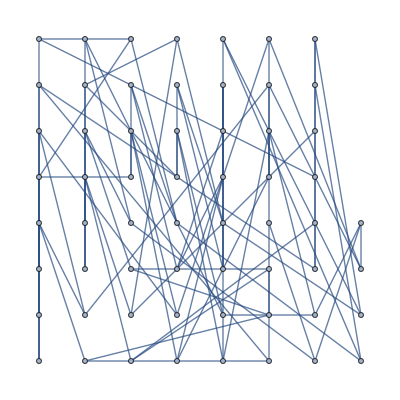
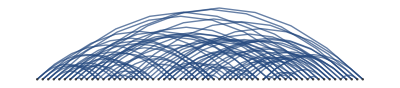
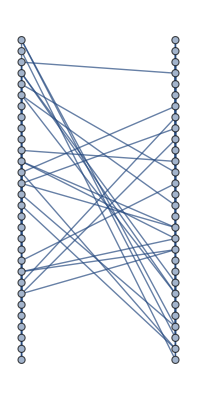
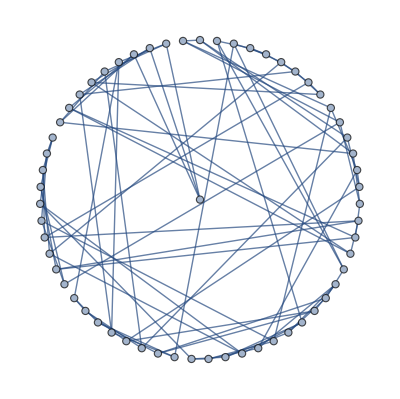
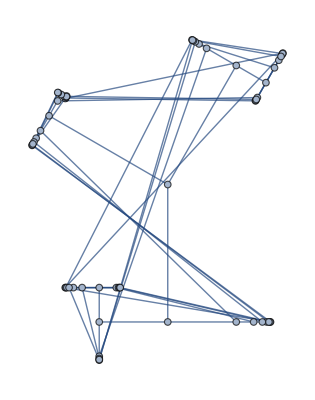
<|BipartiteEmbedding→,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→-Graphics-|>

```mathematica
ApplyGraphEmbeddings[BuckyballGraph[]]
```

Apply the function to a larger buckyball graph:

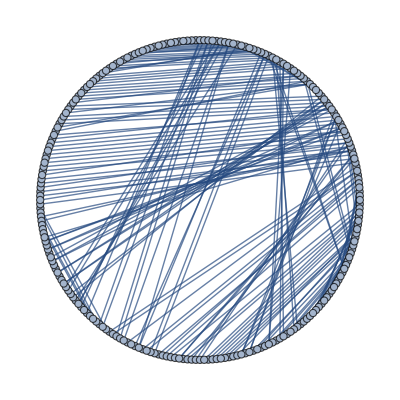
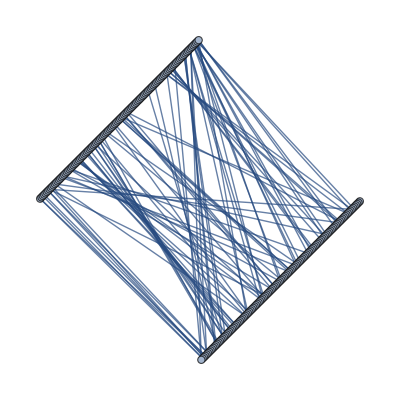
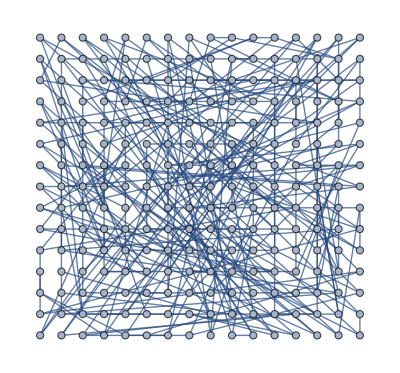
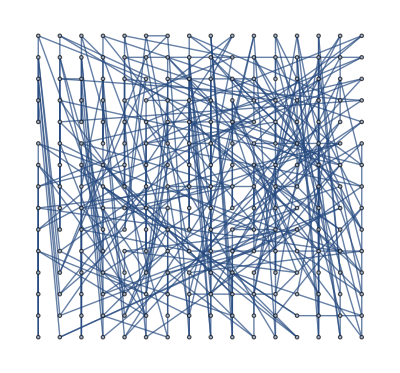
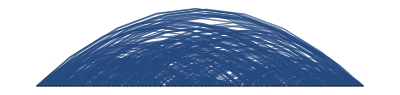
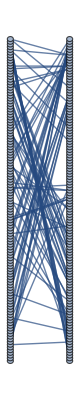
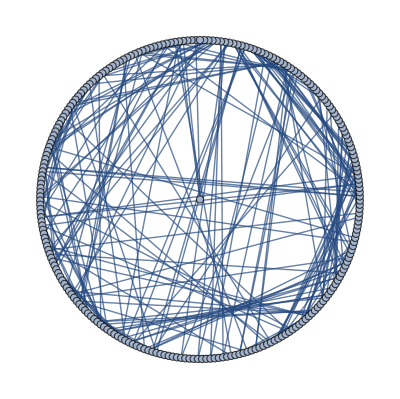
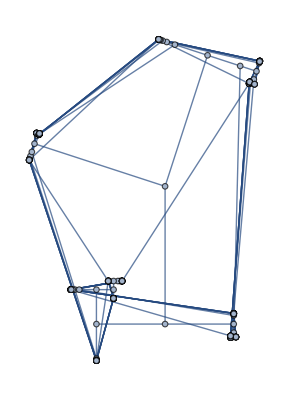
<|BipartiteEmbedding→,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→-Graphics-|>

```mathematica
ApplyGraphEmbeddings[BuckyballGraph[2]]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

View embeddings for a butterfly graph:

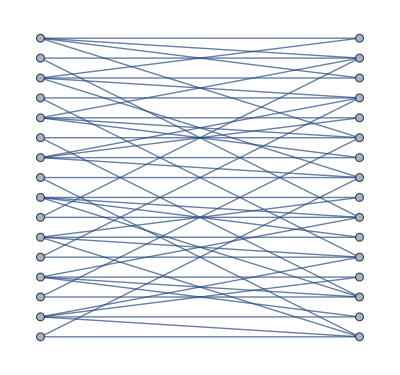
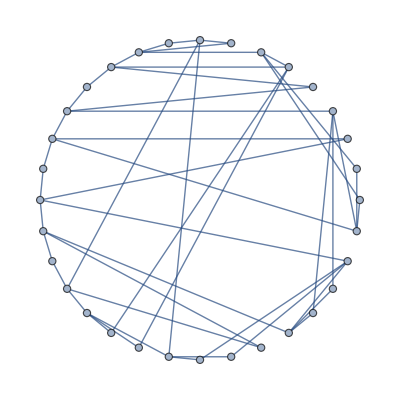
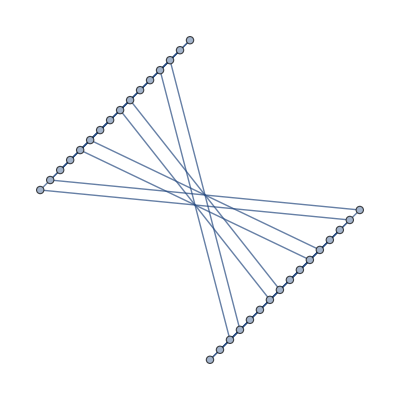
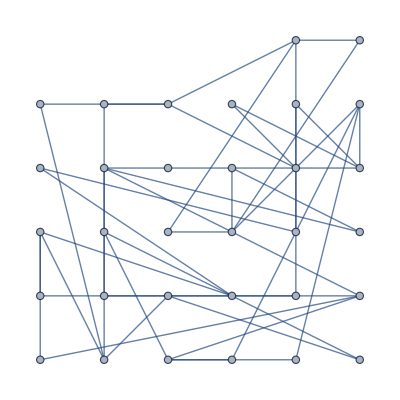
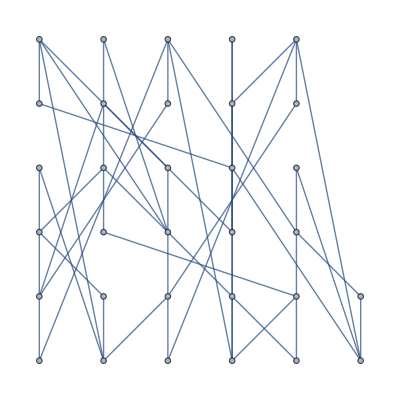
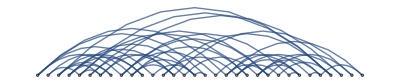
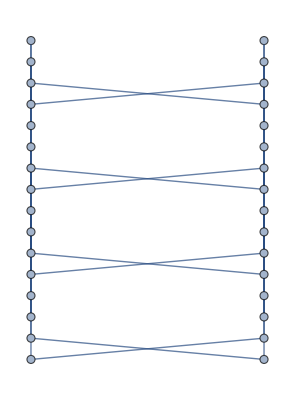
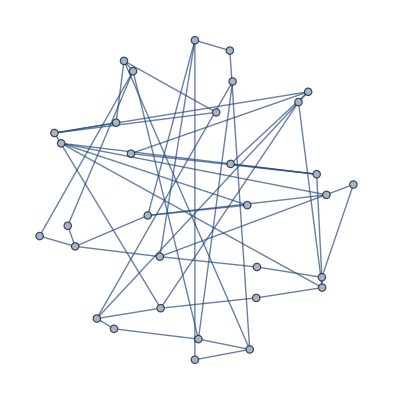
<|BipartiteEmbedding→-Graphics-,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,PlanarEmbedding→,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→|>

```mathematica
ApplyGraphEmbeddings[ButterflyGraph[3,2]]
```

Apply graph embeddings to the torus graph:

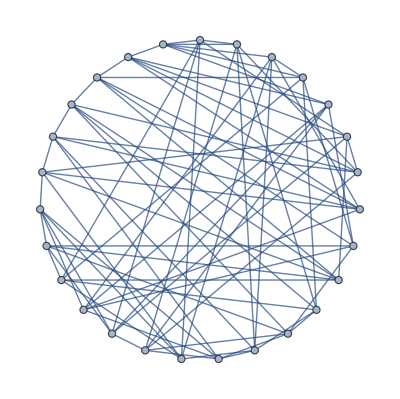
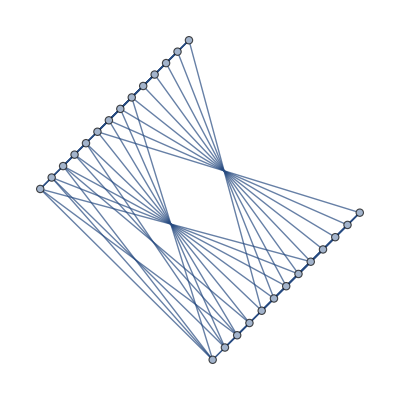
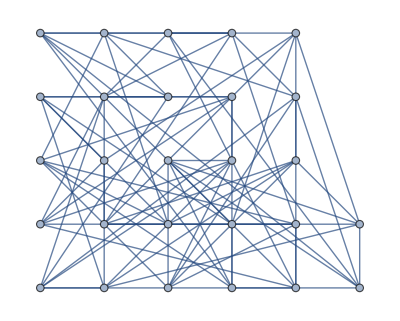
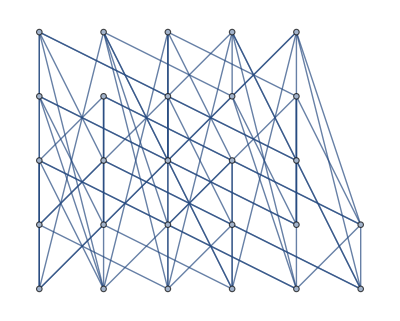
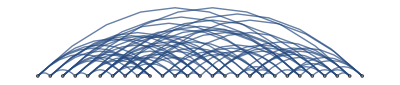
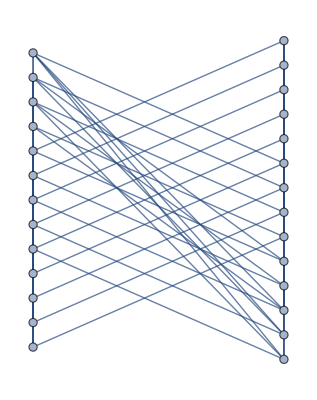
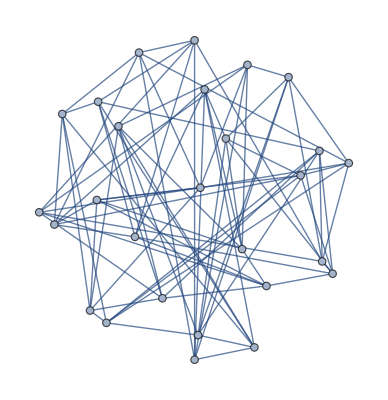
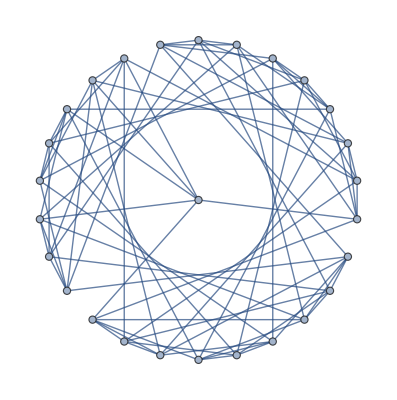
<|BipartiteEmbedding→,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,PlanarEmbedding→,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→|>

```mathematica
ApplyGraphEmbeddings[TorusGraph[{3,3,3}]]
```

### Properties and Relations

Apply graph embeddings to an alternating tree graph using the Resource Function Alternating Tree Graph:

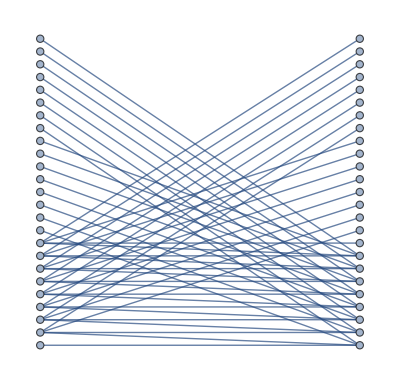
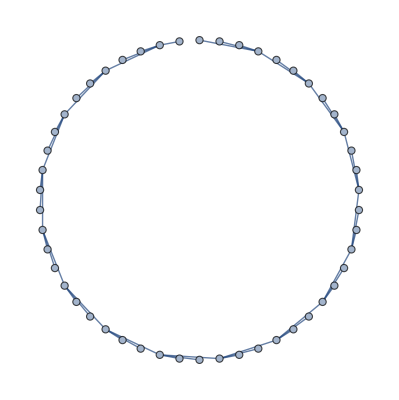
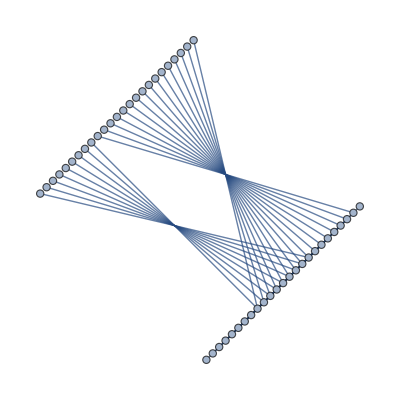
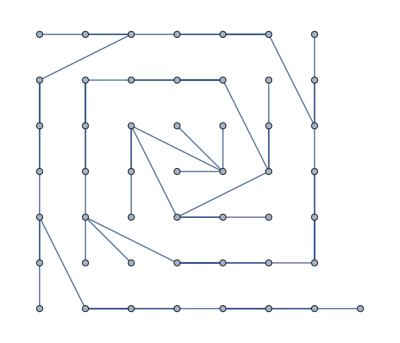
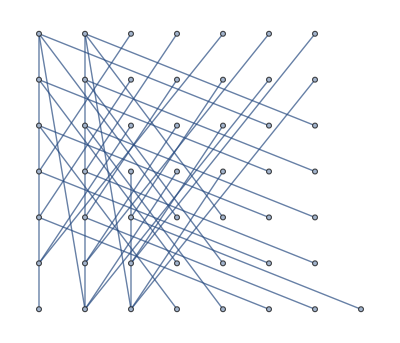
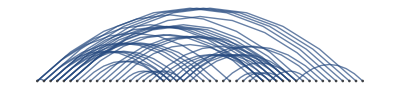
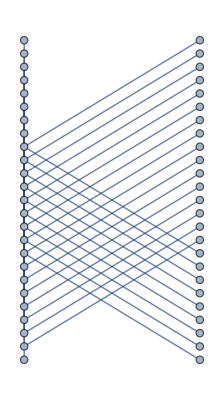
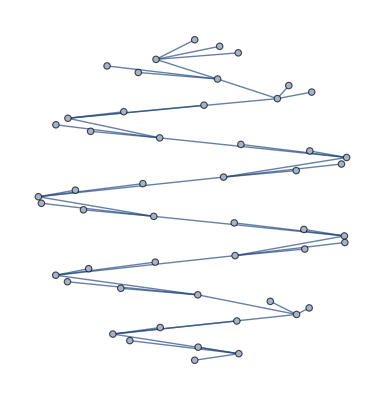
<|BipartiteEmbedding→-Graphics-,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,PlanarEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→-Graphics-|>

```mathematica
ApplyGraphEmbeddings[ResourceFunction["AlternatingTreeGraph"][18]]
```

### Possible Issues

Many of the graph embeddings may be identical:

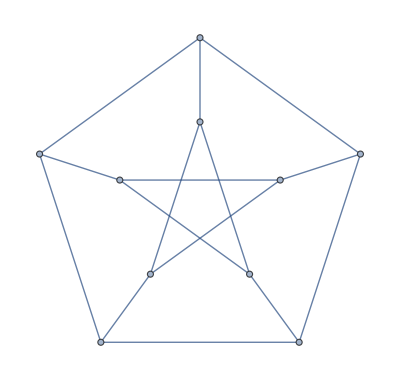
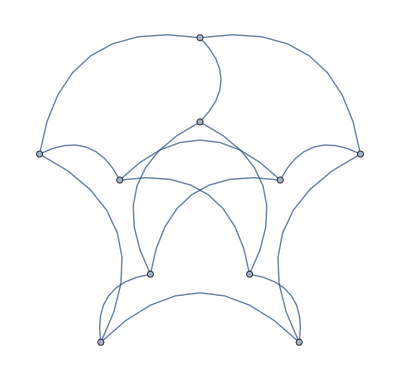
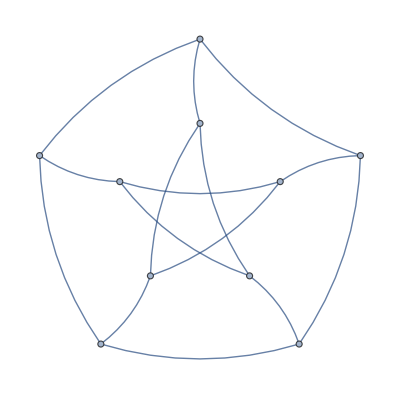
<|BipartiteEmbedding→-Graphics-,CircularEmbedding→-Graphics-,CircularMultipartiteEmbedding→-Graphics-,DiscreteSpiralEmbedding→-Graphics-,GridEmbedding→-Graphics-,LinearEmbedding→-Graphics-,MultipartiteEmbedding→-Graphics-,SpiralEmbedding→-Graphics-,StarEmbedding→-Graphics-,BalloonEmbedding→-Graphics-,RadialEmbedding→-Graphics-,LayeredEmbedding→-Graphics-,GravityEmbedding→-Graphics-,HighDimensionalEmbedding→-Graphics-,PlanarEmbedding→-Graphics-,SpectralEmbedding→-Graphics-,SphericalEmbedding→-Graphics-,SpringElectricalEmbedding→-Graphics-,SpringEmbedding→-Graphics-,TutteEmbedding→-Graphics-|>

```mathematica
ApplyGraphEmbeddings[PetersenGraph[]]
```

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Graph Embeddings

Topological graph theory

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

GraphEmbedding

VertexCoordinates

GraphLayout

Graph3D

GraphPlot

### Related Resource Objects

AlternatingTreeGraph

TriangularGridGraph

HexagonalGridGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

I am working on a function for 3D graph embeddings.